# Elliptic Fracture Surface

Draws the elliptic yield/fracture surface used for ice in (p, q) stress-invariant space:
q(p) = 2 Sqrt[(pmax - p)(p - pmin)] qmax / (pmax - pmin)
and computes q(p = 0), the shear capacity at zero pressure. Edit pMinVal, pMaxVal, qMaxVal (all in Pascals) in the Input cell below and re-evaluate the notebook (Evaluate Notebook, in the Evaluation menu) to try other values.

## Parameters (edit and re-evaluate)

Defaults below match the project's current calibrated values (IceTensileStrength, IceCompressiveStrength, IceShearStrength in simulation.json / base_config.json).

```mathematica
pMinVal = -3.4*10^5;   (* pmin, e.g. -IceTensileStrength; can be negative (tension side) *)
pMaxVal = 30*10^6;      (* pmax, e.g. IceCompressiveStrength *)
qMaxVal = 3.4*10^5;     (* qmax, e.g. IceShearStrength -- peak of the ellipse *)
```

## Elliptic Yield Surface

```mathematica
qEllipse[p_, pmin_, pmax_, qmax_] := 2 Sqrt[Max[0, (pmax - p) (p - pmin)]] qmax/(pmax - pmin)
```

## q at p = 0

```mathematica
qAtZero = N[qEllipse[0, pMinVal, pMaxVal, qMaxVal]];
Print["q(p = 0) = ", qAtZero, " Pa"]
```

q(p = 0) = 71580.3 Pa

```mathematica
-qAtZero/pMinVal
```

0.21053

## Plot

The red point marks (p = 0, q(p = 0)), with dashed guide lines to both axes.

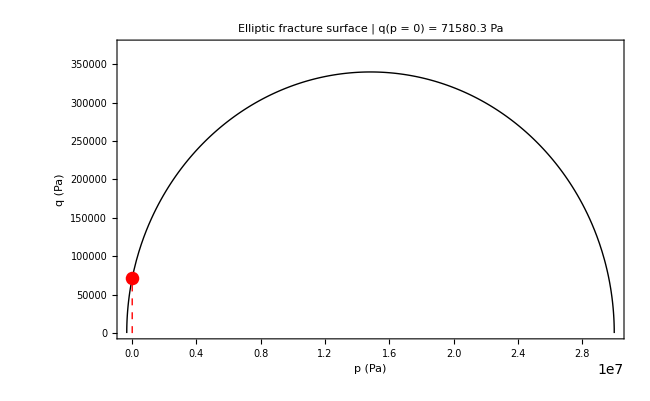

```mathematica
Plot[qEllipse[p, pMinVal, pMaxVal, qMaxVal], {p, pMinVal, pMaxVal},
  PlotRange -> {{pMinVal, pMaxVal}, {0, qMaxVal*1.1}},
  Frame -> True, FrameLabel -> {"p  (Pa)", "q  (Pa)"},
  PlotLabel -> "Elliptic fracture surface   |   q(p = 0) = " <> ToString[NumberForm[qAtZero, 6]] <> " Pa",
  PlotStyle -> Directive[Black, Thick],
  Epilog -> {Red, PointSize[0.015], Point[{0, qAtZero}],
    Dashed, Line[{{0, 0}, {0, qAtZero}}], Line[{{pMinVal, qAtZero}, {0, qAtZero}}]},
  ImageSize -> 650, PlotPoints -> 200]
```